# 1. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Finančna matematika

## Podatki o študentu

Vpišite svoje podatke

Ime: Tatjana

Priimek: Kobe

Vpisna številka: 27214016

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [10 točk]

1. (5 točk) Izračunajte vrsto .

 2. (5 točk) Izračunajte integral

```mathematica
∑_(n=1)^∞ 1/n^2
```

π^2/6

```mathematica
Integrate[√(x/(1-x)), {x, 0, 1}]
```

π/2

## 2. naloga [10 točk]

1. (5 točk) Definirajte funkcijo  f, ki sprejme parametra x in y in ima predpis .
2. (5 točk) Narišite graf implicitno podane funkcije, ko je   za  in  .

```mathematica
ClearAll[x,y]
ClearAll[x]
```

```mathematica
f[x_,y_]:=(x^2+y^2)^2-y^2-x(x^2+y^2)
```

```mathematica
FindRoot[f[x,y]==0, {x, -2,2}, {y,-2,2}]
```

FindRoot::nveq: The number of equations does not match the number of variables in FindRoot[f[x,y]==0,{x,-2,2},{y,-2,2}].

FindRoot[f[x,y]==0,{x,-2,2},{y,-2,2}]

```mathematica
x/. Solve[f[x,y]==0]
```

{x,x,x,x}

```mathematica
x/. Solve[f[x,y]==0, {{x,-2,2}{y,-2,2}}]
```

Solve::ivar: {x y,4,4} is not a valid variable.

ReplaceAll::reps: {Solve[-y^2-x (x^2+y^2)+(x^2+y^2)^2==0,{{x y,4,4}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.Solve[-y^2-x (x^2+y^2)+(x^2+y^2)^2==0,{{x y,4,4}}]

```mathematica
Plot[f[x,y],{x,-2,2},{y,-2,2}]
```

Plot::nonopt: Options expected (instead of {y,-2,2}) beyond position 2 in Plot[f[x,y],{x,-2,2},{y,-2,2}]. An option must be a rule or a list of rules.

Plot[f[x,y],{x,-2,2},{y,-2,2}]

```mathematica
NSolve[f[x,y]==0,{x,y},{x,y}∈Interval[{−2,2}]]
```

NSolve::bdomv: Warning: {x,y}∈Interval[{-2,2}] is not a valid domain specification. Assuming it is a variable to eliminate.

NSolve::disj: Variable lists {x,y} and {x,y} should be disjoint.

NSolve[-y^2-x (x^2+y^2)+(x^2+y^2)^2==0,{x,y},{x,y}∈Interval[{-2,2}]]

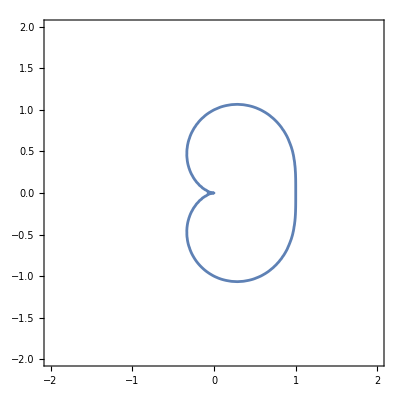

```mathematica
ContourPlot[f[x,y]==0,{x,-2,2},{y,-2,2}]
```

```mathematica
Plot[f[x,y]==0,{x,-2,2},{y,-2,2}]
```

Plot::nonopt: Options expected (instead of {y,-2,2}) beyond position 2 in Plot[f[x,y]==0,{x,-2,2},{y,-2,2}]. An option must be a rule or a list of rules.

Plot[f[x,y]==0,{x,-2,2},{y,-2,2}]

## 3. naloga [10 točk]

1. (4 točke) V spremenljivko potence shranite vse lihe potence števila 2 od 1 do 25, od katerih odštejete 1: 1, 7, 31, 127 ... Pomagajte si z ukazom Table.
2. (4 točke) Izberite vsa števila iz seznama potenc, ki so praštevila. 
3. (2 točki) Naredite enako še za sode potence.

```mathematica
ClearAll[n]
potence= Table[2^n-1,{n,1,25}, Mod[n, 2]== 1]
```

Table::nliter: Non-list iterator Mod[n,2]==1 at position 3 does not evaluate to a real numeric value.

Table[2^n-1,{n,1,25},Mod[n,2]==1]

```mathematica
potence= Table[2^n-1, {n,1,25,2}]
```

{1,7,31,127,511,2047,8191,32767,131071,524287,2097151,8388607,33554431}

```mathematica
Select[potence, PrimeQ]
```

{7,31,127,8191,131071,524287}

```mathematica
ClearAll[n]
```

```mathematica
potence2=Table[2^n-1,{n,2,25, 2}]
```

{3,15,63,255,1023,4095,16383,65535,262143,1048575,4194303,16777215}

```mathematica
Select[potence2, PrimeQ]
```

{3}